## P2.2

### Part b

#### Clear main context

```mathematica
Clear["`*"]
```

#### Solve the equation

```mathematica
s = NDSolve[{y''[x] + Sin[x]y'[x] + Exp[x]y[x] == x^2, y[0] == 0, y[5]==3}, y, {x, 0, 5}];
```

#### Plot the solution

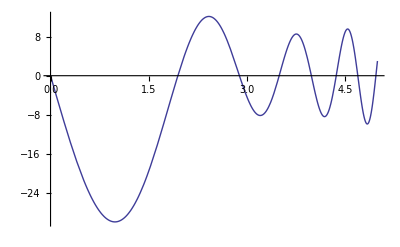

```mathematica
Plot[Evaluate[y[x]/.s], {x, 0, 5}, PlotRange->All]
```

#### Evaluate at x = 4.5

```mathematica
Evaluate[y[x]/.s]/.x->4.5
```

{8.72062}